```mathematica
strm := strm = OpenRead["/tmp/correctQ"]

readLine[] :=
	Module[{line = Read[strm, String]},
		If[StringQ[line],
			line,
			$Failed
		]
	]

nextEntry[] :=
	Module[{line, entry = ""},
		line = readLine[];
		While[StringQ[line] && line != "}",
			 entry = entry <> line;
			 line = readLine[]
		];
		If[StringQ[line],
			entry = ImportString[entry <> "}", "JSON"],
			entry = $Failed
		];
		entry
	]
```

```mathematica
entry=nextEntry[];
entries={};
```

```mathematica
While[ListQ[entry],
AppendTo[entries,entry];
entry=nextEntry[];
];
```

```mathematica
entries=Select[entries,StringLength["user"/.#]<10&];
```

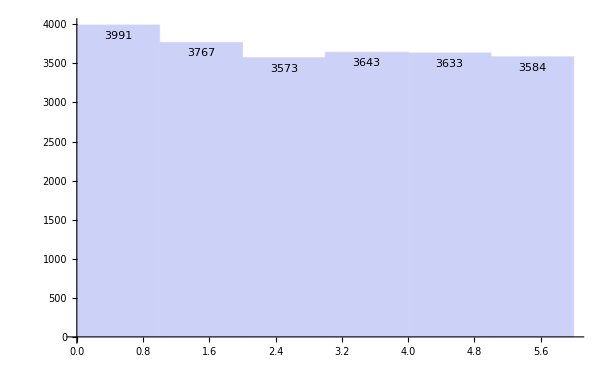

```mathematica
Histogram[ToExpression[First[#]]&/@Select[Flatten@("correctQ"/.entries),TrueQ[Last[#]]&],LabelingFunction->Top]
```

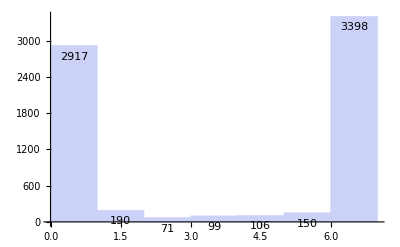
-Graphics-Histogram of number of correct answers. 3398 got all datasets correct at some point, while 2997 did not get any correct.

```mathematica
Labeled[
Histogram[
Table[Count[Last/@entry,True],{entry,("correctQ"/.entries)}],
LabelingFunction->Top
],
"Histogram of number of correct answers. 3398 got all datasets correct at some point, while 2997 did not get any correct."
]
```

```mathematica
full=Select[entries,Count[Last/@("correctQ"/.#),True]==6&];
```

```mathematica
Manipulate[
Module[{elem=full[[ii]]},
Grid[{
{"index",ii},
{"user","user"/.elem},
{"correct#",Count[Last/@("correctQ"/.elem),True]},
{"program","program"/.elem}
}]
],
{ii,1,Length[full],1}
]
```

```mathematica
Export["/tmp/distribution.png",-Graphics-]
```

/tmp/distribution.png